## 2MBA50 Mathematica Practicum 1 exercises

This series of notebooks is made in Mathematica 13.3.

Contact: Jan Willem Knopper, MF 5.121, jw.knopper@tue.nl
Author: ir. W.J.P.M. Kortsmit, small adjustments by Benne de Weger, Jan Willem Knopper.

## 1. Basic principles

### Name:

### Exercises

Give your answers in this notebook in the empty which appears after each header “Answer” when you open that cell group. Do not mess with the text of the exercises.

Using copy and paste with Mathematica expressions can be a somewhat tricky business, caused by the presentation form of some of those expressions. If any issues arise, just retype the expressions, this also gives more practice in working with Mathematica.

#### Exercise 1.1

Assign the expression x^3/7+x^2/5+6 x-11/21 to f. 
a) Draw the graph of f for -10≤x≤10 by using the command Plot.
b) Compute f in the point x=3/7. Use the substitution rules for this.
c) Do the same for x=-3/7.

#### Answer

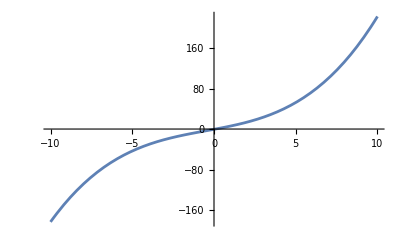

75473/36015

-110557/36015

```mathematica
f:=x^3/7 + x^2/5 +6x - 11/21
Plot[f,{x,-10,10}]
f/.x->3/7
f /. x -> -3/7
```

#### Exercise 1.2

Calculate the expression x^2 y^2 sin(x y z) in the point (x,y,z)=(3,2,1) without using assignments.

#### Answer

```mathematica
x^2*y^2*Sin[x*y*z] /. {x->3, y -> 2, z->1}
```

36 Sin[6]

#### Exercise 1.3

Predict the result of each of the following instructions. Then execute them.
	a) f=x^2 y^2+x+2 y
	b) f/.{x→1,y→x}
	c) f/.{y→x,x→1}
	Clear[f]

#### Answer

```mathematica
f = x^2y^2+x+2y
f /. {x->1, y->x}
f /. {y->x, x->1}
Clear[f]
```

x+2 y+x^2 y^2

1+2 x+x^2

1+2 x+x^2

#### Exercise 1.4

Look up the concept Prime by using the helper function. 
How big is the one hundred millionth prime number?

#### Answer

```mathematica
Prime[100000000]
```

2038074743

#### Exercise 1.5

Give the numerical value of ...  to 100 decimal places.
a) π
b) sin(3)

#### Answer

```mathematica
N[Pi, 101]
N[Sin[3], 100]
```

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

0.1411200080598672221007448028081102798469332642522655841518826412324220099670144719112821728534498638

#### Exercise 1.6

a) Evaluate the following substitution rule (2 √2+√3)/(√2)/.√2→w
b) Look up the function FullForm in the Mathematica Help, and apply this to (2 √2+√3)/(√2). 
The FullForm shows you how the formula is internally represented in Mathematica. Look at the output.
c) Can you explain why the substitution rule does not fully work?

#### Answer

```mathematica
(2Sqrt[2] + Sqrt[3])/Sqrt[2] /. Sqrt[2] -> w
FullForm[(2Sqrt[2] + Sqrt[3])/Sqrt[2]]
"The substitution doesn't work because the square root in the denominator is represented as Power[2, Rational[-1,2]] and the substitution replaces all occurences of Power[2, Rational[1,2]."
```

(√3+2 w)/(√2)

Times[Power[2,Rational[-1,2]],Plus[Times[2,Power[2,Rational[1,2]]],Power[3,Rational[1,2]]]]

The substitution doesn't work because the square root in the denominator is represented as Power[2, Rational[-1,2]] and the substitution replaces all occurences of Power[2, Rational[1,2].